# ListDensityPlot del indicador de caos 𝒫̄ [Mirkin y Wisniacki 2021]

```mathematica
SetDirectory[NotebookDirectory[]];
```

## L=3

```mathematica
L=3; 
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],chaometerPurity=#[[2;;]];}&[Import["data/chaometer_purity/wisniacki_open_L_"<>ToString[L]<>"_hx_1.csv"]]
```

{{hz,J,pureza del caometro (indicador de Wisniacki)},Null}

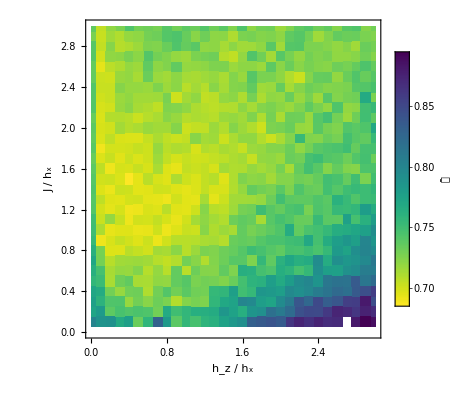

```mathematica
fontSize=18;

fig=ListDensityPlot[chaometerPurity,
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->{Min[chaometerPurity[[All,3]]],Max[Select[chaometerPurity[[All,3]],#<1&]]},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"𝒫̄",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
filename="figs_ja/chaometer_purity/wisniacki_open_L_"<>ToString[L]<>"_hx_1.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
```

figs_ja/chaometer_purity/wisniacki_open_L_3_hx_1.pdf

```mathematica
RunProcess[{"pdfcrop",filename,filename}]
```

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `figs_ja/chaometer_purity/wisniacki_open_L_3_hx_1.pdf'.
,StandardError→|>

## L=4

```mathematica
L=4; 
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],chaometerPurity=#[[2;;]];}&[Import["data/chaometer_purity/wisniacki_open_L_"<>ToString[L]<>"_hx_1.csv"]]
```

{{hz,J,promedio temporal de 0 a 100 de la pureza del caometro},Null}

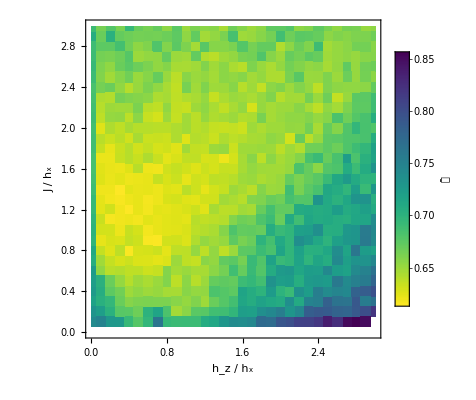

```mathematica
fontSize=18;

fig=ListDensityPlot[chaometerPurity,
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->{Min[chaometerPurity[[All,3]]],Max[Select[chaometerPurity[[All,3]],#<1&]]},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"𝒫̄",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
filename="figs_ja/chaometer_purity/wisniacki_open_L_"<>ToString[L]<>"_hx_1.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
```

figs_ja/chaometer_purity/wisniacki_open_L_4_hx_1.pdf

```mathematica
RunProcess[{"pdfcrop",filename,filename}]
```

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `figs_ja/chaometer_purity/wisniacki_open_L_4_hx_1.pdf'.
,StandardError→|>

## L=5

```mathematica
L=5; 
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],chaometerPurity=#[[2;;]];}&[Import["data/chaometer_purity/wisniacki_open_L_"<>ToString[L]<>"_hx_1.csv"]]
```

{{hz,J,promedio temporal de 0 a 100 de la pureza del caometro},Null}

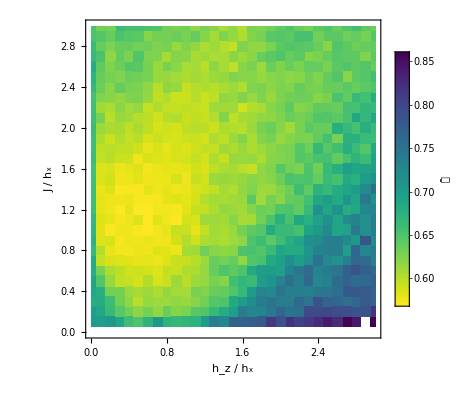

```mathematica
fontSize=18;

fig=ListDensityPlot[chaometerPurity,
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->{Min[chaometerPurity[[All,3]]],Max[Select[chaometerPurity[[All,3]],#<1&]]},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"𝒫̄",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
filename="figs_ja/chaometer_purity/wisniacki_open_L_"<>ToString[L]<>"_hx_1.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
```

figs_ja/chaometer_purity/wisniacki_open_L_5_hx_1.pdf

```mathematica
RunProcess[{"pdfcrop",filename,filename}]
```

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `figs_ja/chaometer_purity/wisniacki_open_L_5_hx_1.pdf'.
,StandardError→|>

## L=6

```mathematica
L=6; 
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],chaometerPurity=#[[2;;]];}&[Import["data/chaometer_purity/wisniacki_open_L_"<>ToString[L]<>"_hx_1.csv"]]
```

{{hz,J,pureza del caometro (indicador de Wisniacki)},Null}

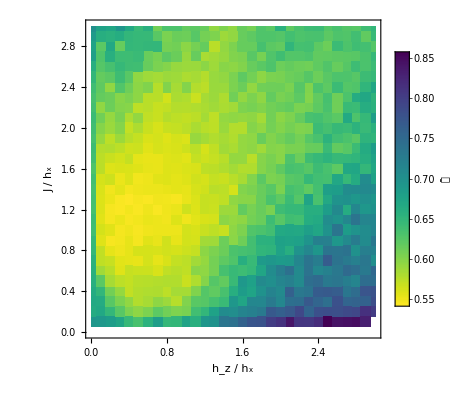

```mathematica
fontSize=18;

fig=ListDensityPlot[chaometerPurity,
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->{Min[chaometerPurity[[All,3]]],Max[Select[chaometerPurity[[All,3]],#<1&]]},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"𝒫̄",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
filename="figs_ja/chaometer_purity/wisniacki_open_L_"<>ToString[L]<>"_hx_1.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
```

figs_ja/chaometer_purity/wisniacki_open_L_6_hx_1.pdf

```mathematica
RunProcess[{"pdfcrop",filename,filename}]
```

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `figs_ja/chaometer_purity/wisniacki_open_L_6_hx_1.pdf'.
,StandardError→|>

## L=7

```mathematica
L=7; 
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],chaometerPurity=#[[2;;]];}&[Import["data/chaometer_purity/wisniacki_open_L_"<>ToString[L]<>"_hx_1.csv"]]
```

{{hz,J,pureza del caometro (indicador de Wisniacki)},Null}

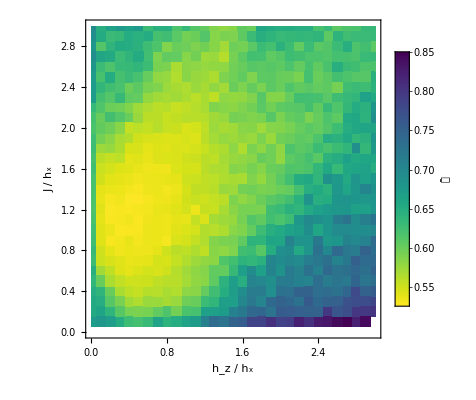

```mathematica
fontSize=18;

fig=ListDensityPlot[chaometerPurity,
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->{Min[chaometerPurity[[All,3]]],Max[Select[chaometerPurity[[All,3]],#<1&]]},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"𝒫̄",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
filename="figs_ja/chaometer_purity/wisniacki_open_L_"<>ToString[L]<>"_hx_1.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
```

figs_ja/chaometer_purity/wisniacki_open_L_7_hx_1.pdf

```mathematica
RunProcess[{"pdfcrop",filename,filename}]
```

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `figs_ja/chaometer_purity/wisniacki_open_L_7_hx_1.pdf'.
,StandardError→|>